## Optimizations

## Matrix

```mathematica
Quit[]
```

```mathematica
<<Q3`Quisso`
```

Q3/Cauchy.m v1.4 (2020-10-30) Mahn-Soo Choi

Q3/Pauli.m v1.4 (2020-10-30) Mahn-Soo Choi

Q3/Quisso.m v1.4 (2020-10-30) Mahn-Soo Choi

```mathematica
Let[Qubit,S]
```

```mathematica
$N=8;
NN=Range[$N];
SS=S[NN,None]
bs=Basis@SS;
vv=RandomComplex[{-1-I,1+I},Length@bs];
expr=bs.vv;
```

{S_1,S_2,S_3,S_4,S_5,S_6,S_7,S_8}

```mathematica
Timing[v1=Matrix[expr];]
```

{0.276567,Null}

```mathematica
$N=5;
SS=S[Range[$N],None];
op=Multiply@@@Tuples[Table[S[j,Full],{j,1,$N}]];
vv=RandomComplex[(1+I){-1,1},Length@op];
expr=vv.op;
```

```mathematica
Timing[m1=Matrix[expr];]
```

{0.367316,Null}

```mathematica
Timing[expr2=QuissoExpression[m1,SS];]
```

{19.4912,Null}

```mathematica
expr2-expr//QuissoExpand//Garner//Chop
```

0

## Physical Examples

## Example: Quantum Teleportation

```mathematica
Quit[]
```

```mathematica
<<Quaphy`Quisso`
```

Quaphy/Quisso.wl v8.4 (2020-04-06) Mahn-Soo Choi

```mathematica
Let[Qubit,S]
```

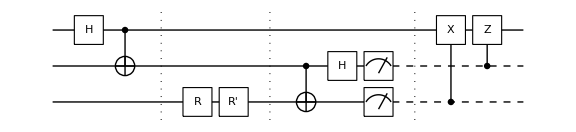

```mathematica
Rz=Rotation[S[3,3],Pi/3,Label->"R"];
Ry=Rotation[S[3,2],Pi/6,Label->Superscript["R",′]];
qc=QuissoCircuit[
Ket[],
S[1,6],CNOT[S[1],S[2]],"Separator",
Rz,Ry,"Separator",
CNOT[S[2],S[3]],
S[2,6],{Measure[S[2]],Measure[S[3]]},"Separator",
Controlled[S[3],S[1,1]],
Controlled[S[2],S[1,3]]
];
gr=Graphics[qc,ImageSize->Large]
```

Converting the QuissoCircuit to Quisso expression,

```mathematica
out=QuissoExpression[qc]//Simplify
w=QuissoFactor[out,S[{2,3}]]//Simplify;
w//LogicalForm
v=Rz**Ry**Ket[]//Simplify;
LogicalForm[v]
```

((1/4+ⅈ/4) (((-2+ⅈ)+√3) 1_S_11_S_21_S_3+ⅈ ((2+ⅈ)+√3) 1_S_21_S_3))/(√2)

1_S_21_S_3⊗(((1/4+ⅈ/4) (ⅈ ((2+ⅈ)+√3) 0_S_1+((-2+ⅈ)+√3) 1_S_1))/(√2))

((1/4-ⅈ/4) (((2+ⅈ)+√3) 0_S_3+((2+ⅈ)-√3) 1_S_3))/(√2)

```mathematica
val=Table[
out=QuissoExpression[qc]//Simplify;
Readout[S[{2,3}],out],
{50}
];
Histogram3D[val]
```

-Graphics3D-

Explicitly constructing the Quisso expression,

```mathematica
vec=Multiply[
Controlled[S[2],S[1,3]],
Controlled[S[3],S[1,1]],
Measure[S[2]][Measure[S[3]][
Simplify@Multiply[S[2,6],
CNOT[S[2],S[3]],
Rz,Ry,
CNOT[S[1],S[2]],
S[1,6],
Ket[S[{1,2,3}]->1]]]]]//Simplify;
QuissoFactor[vec,S[{2,3}]]
orig=Rz**Ry**Ket[]//Simplify
```

0_S_21_S_3⊗(((1/4+ⅈ/4) (((-2+ⅈ)-√3) ␣+((-2+ⅈ)+√3) 1_S_1))/(√2))

((1/4-ⅈ/4) (((2+ⅈ)+√3) ␣+((2+ⅈ)-√3) 1_S_3))/(√2)

## Example: One-Way Computation I

```mathematica
Quit[]
```

```mathematica
<<Quaphy`Quisso`
```

Quaphy/Quisso.wl v8.22 (2020-04-14) Mahn-Soo Choi

```mathematica
Let[Qubit,S]
```

```mathematica
Let[Real,α,β,γ]
Let[Complex,c]
```

```mathematica
R0=Rotation[S[0,3],α,Label->"R"];
v0=ProductState[S[0]->{c[0],c[1]},S[1]->{1,0}]
rules={c[{0,1}].Dagger@c[{0,1}]->1};
```

(c_0 0+c_1 1)_S_0⊗(0)_S_1

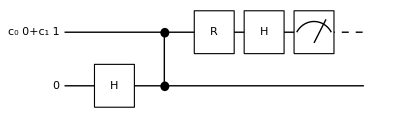

```mathematica
qc=QuissoCircuit[
v0,
S[1,6],
CZ[S[0],S[1]],R0,
S[0,6],Measure[S[0]]
];
g=Graphics[qc]
```

```mathematica
v=QuissoExpression[qc]
```

(1_S_01_S_1 ((c_0+c_1) Cos[α/2]-ⅈ (c_0-c_1) Sin[α/2]))/(√2 √(c_0 c_0^*+c_1 c_1^*))+(1_S_0 ((c_0-c_1) Cos[α/2]-ⅈ (c_0+c_1) Sin[α/2]))/(√2 √(c_0 c_0^*+c_1 c_1^*))

```mathematica
v=v/.rules//Simplify//LogicalForm;
vv=QuissoFactor[v,S[0]]//Simplify
w=vv[[2]]
```

1_S_0⊗((1_S_1 ((c_0+c_1) Cos[α/2]-ⅈ (c_0-c_1) Sin[α/2])+0_S_1 ((c_0-c_1) Cos[α/2]-ⅈ (c_0+c_1) Sin[α/2]))/(√2))

(1_S_1 ((c_0+c_1) Cos[α/2]-ⅈ (c_0-c_1) Sin[α/2])+0_S_1 ((c_0-c_1) Cos[α/2]-ⅈ (c_0+c_1) Sin[α/2]))/(√2)

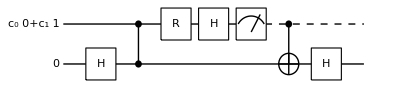

```mathematica
qc=QuissoCircuit[
v0,
S[1,6],
CZ[S[0],S[1]],
R0,S[0,6],
Measure[S[0]],
CNOT[S[0],S[1]],
S[1,6]
]
```

```mathematica
v1=LogicalForm[QuissoExpression[qc]/.rules,S[{0,1}]]//Simplify
v1=QuissoFactor[v1,S[0]][[2]]
```

c_0 1_S_00_S_1 (Cos[α/2]-ⅈ Sin[α/2])+c_1 1_S_01_S_1 (Cos[α/2]+ⅈ Sin[α/2])

c_0 0_S_1 (Cos[α/2]-ⅈ Sin[α/2])+c_1 1_S_1 (Cos[α/2]+ⅈ Sin[α/2])

```mathematica
v2=Rotation[S[1,3],α]**ProductState[S[1]->c[{0,1}]];
v2-v1//DefaultForm//Simplify
```

0

## Example: One-Way Computation II

```mathematica
Quit[]
```

```mathematica
<<Quaphy`Quisso`
```

Quaphy/Cauchy.wl v8.2 (2020-04-06) Mahn-Soo Choi

Quaphy/Pauli.wl v8.7 (2020-04-07) Mahn-Soo Choi

Quaphy/Quisso.wl v8.5 (2020-04-07) Mahn-Soo Choi

```mathematica
Let[Qubit,S]
```

```mathematica
Let[Real,α,β,γ]
Let[Complex,c]
```

```mathematica
R1=Rotation[S[1,3],α,Label->"R"];
R2=Rotation[S[2,3],β,Label->Superscript["R",′]];
R3=Rotation[S[3,3],γ,Label->Superscript["R",″]];
```

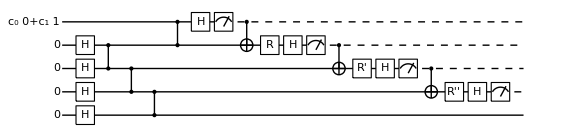

```mathematica
qc=QuissoCircuit[
ProductState[S[0]->{c[0],c[1]},S[{1,2,3,4}]->{1,0}],
S[{1,2,3,4},6],
CZ[S[1],S[2]],CZ[S[2],S[3]],CZ[S[3],S[4]],
CZ[S[0],S[1]],
S[0,6],Measure[S[0]],
CNOT[S[0],S[1]],R1,
S[1,6],Measure[S[1]],
CNOT[S[1],S[2]],R2,
S[2,6],Measure[S[2]],
CNOT[S[2],S[3]],R3,
S[3,6],Measure[S[3]]
];
g=Graphics[qc,ImageSize->Large]
```

```mathematica
Timing[expr=QuissoExpression[qc]/.{c[0]Conjugate[c[0]]+c[1]Conjugate[c[1]]->1}]
```

{17.5494,1/2 1_S_3 (c_0 Cos[1/2 (α-β-γ)]-c_0 Cos[1/2 (α+β-γ)]+c_1 Cos[1/2 (α-β+γ)]+c_1 Cos[1/2 (α+β+γ)]-ⅈ c_1 Sin[1/2 (α-β-γ)]+ⅈ c_1 Sin[1/2 (α+β-γ)]-ⅈ c_0 Sin[1/2 (α-β+γ)]-ⅈ c_0 Sin[1/2 (α+β+γ)])+1/2 1_S_31_S_4 (-c_1 Cos[1/2 (α-β-γ)]+c_1 Cos[1/2 (α+β-γ)]+c_0 Cos[1/2 (α-β+γ)]+c_0 Cos[1/2 (α+β+γ)]+ⅈ c_0 Sin[1/2 (α-β-γ)]-ⅈ c_0 Sin[1/2 (α+β-γ)]-ⅈ c_1 Sin[1/2 (α-β+γ)]-ⅈ c_1 Sin[1/2 (α+β+γ)])}

```mathematica
ss=S[Range[0,4],]
LogicalForm[expr,ss]//Simplify
```

{S_0,S_1,S_2,S_3,S_4}

1/2 (0_S_00_S_10_S_21_S_30_S_4 (c_0 Cos[1/2 (α-β-γ)]-c_0 Cos[1/2 (α+β-γ)]+c_1 Cos[1/2 (α-β+γ)]+c_1 Cos[1/2 (α+β+γ)]-ⅈ c_1 Sin[1/2 (α-β-γ)]+ⅈ c_1 Sin[1/2 (α+β-γ)]-ⅈ c_0 Sin[1/2 (α-β+γ)]-ⅈ c_0 Sin[1/2 (α+β+γ)])+0_S_00_S_10_S_21_S_31_S_4 (-c_1 Cos[1/2 (α-β-γ)]+c_1 Cos[1/2 (α+β-γ)]+c_0 Cos[1/2 (α-β+γ)]+c_0 Cos[1/2 (α+β+γ)]+ⅈ c_0 Sin[1/2 (α-β-γ)]-ⅈ c_0 Sin[1/2 (α+β-γ)]-ⅈ c_1 Sin[1/2 (α-β+γ)]-ⅈ c_1 Sin[1/2 (α+β+γ)]))